## Partition coefficient file creation. Requires minimal input for initial guesses for coefficients, acceptable ranges, and max iterations out of all programs I tested for convergence.

#### Import your partition values from an excel file. Assumes the first column is temperature and the second is Q(T) from the catalog. Click on each cell next to the code, then hit shift+enter to run each cell in this script.

Replace the path name with the location of your file. It needs double back slashes between directory names.

C:\Users\heath\Documents\Research\Observing-laptop\Gobasic\CatalogFile\C2H5OH.xlsx

{{{300.,45601.3},{250.,33853.1},{225.,28439.9},{180.,19556.},{150.,14312.3},{120.,9684.05},{75.,4106.4},{37.5,1072.42},{18.75,290.946},{9.375,95.597},{5.,37.5425},{2.725,15.4354}}}

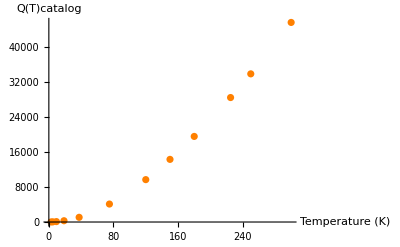

```mathematica
path="C:\\Users\\heath\\Documents\\Research\\Observing-laptop\\Gobasic\\CatalogFile\\C2H5OH.xlsx"
s=Import[path]
ListPlot[s[[1]],PlotStyle->Orange,AxesLabel->{"Temperature (K)","Q(T)catalog"}]
```

This is where you would change B, C, and D to be 1, 1.5, or 0 to simplify the expression if it makes the fit better (if you change B, C, or D to a fixed value, you will need to delete that letter from the listed variables right after the equation, where it says {a,b,c,d}). Run the cell below and check the fit to see if looks okay. Check the percent error and the δ% values at the end to make your final decision on the best fit. Record the max and min percent error and/or δ% values, as you will have to report these later if they are not already reported in previous papers.

{a→6.72124,b→1.49877,d→-60.0823,c→0.496432}

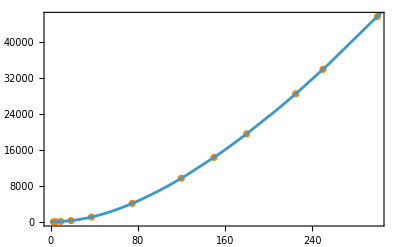

Max percent error =

2.88075

Min percent error =

0.000735443

Max δ% =

0.359663

Min δ% =

-2.88075

```mathematica
nlm=NonlinearModelFit[s[[1]],{a*(x^b)*(c+Exp[d/x])},{a,b,d,c},x,MaxIterations->∞];
nlm["BestFitParameters"]
Show[ListPlot[s[[1]],PlotStyle->Orange],Plot[nlm[x],{x,0,5000}],Frame->True]
nlm["PredictedResponse"];
temp=Import[path,{"Data",1,All,1}];
qt=Import[path,{"Data",1,All,2}];
percenterror=(Abs[qt-nlm["PredictedResponse"]]/qt)*100;
Print["Max percent error ="] 
Max[percenterror]
Print["Min percent error ="] 
Min[percenterror]
deltapercent=((nlm["PredictedResponse"]/qt)-1)*100;
Print["Max δ% ="] 
Max[deltapercent]
Print["Min δ% ="] 
Min[deltapercent]
```

Once satisfied with your a, b, c, and d partition coefficients, copy the output from the Mathematica cell over to a new text file and save it as molecule.co file.
Refer to other co files for syntax.